# Analysis of Triangle Completion Categorical experiment

## Loading the data and functions

```mathematica
SetDirectory["/home/uvhart/GitHubLib/EuclideanGeoSurvey"];
```

```mathematica
SetDirectory["/Users/alcarden4/Desktop/WebstormProjects/EuclideanGeoSurvey"]
```

```mathematica
Needs["ErrorBarPlots`"];
LogFilePilot1=DeleteCases[Import["logVertexCat.txt","Table"],Except[{___,"ERROR",___}]];
```

```mathematica
LogFilePilot1;
```

```mathematica
temp=Select[DATASort,#[[5,5]]≠"9999"&];
```

```mathematica
Length@temp
```

9

#### Data

```mathematica
DataUnCln={LogFilePilot1[[;;,;;2]],LogFilePilot1[[;;,6;;]]}ᵀ;
DATA=Join[#[[1]],If[Length[#[[2]]]==1,StringSplit[#[[2,1]],"_"],Join[StringSplit[#[[2,1]],"_"],#[[2,2;;]]]]]&/@DataUnCln;
DATASort=Select[Select[GatherBy[DATA,#[[3]]&],Length@#>120&],#[[5,5]]≠"9999"&];
DataClean=SortBy[#,#[[{1,2}]]&]&@GatherBy[Select[#,StringContainsQ[#[[5]],"Run"]&][[2;;,{7,9,11,12,13,15,17,19}]],#[[{1,2}]]&]&/@DATASort;
(*7=angle; 9=base factor; 11=Qtype; 12=Manipulation; 13=What's manipulated; 15=correct answer; 17=timing; 19=user answer;*)
DataClnGraded=Join@@@Map[Append[#,If[#[[6]]==#[[8]],1,0]]&,DataClean,{3}];
```

### Percent correct vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

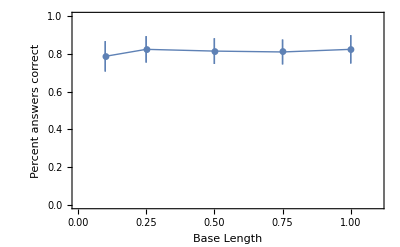

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,1.1},{0,1}},Frame-> {True,True,False,False},FrameLabel->{"Base Length","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,2]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{2}]]&]&/@DataClnGraded,{2,1,3}])
```

### Percent correct vs. Angle Size

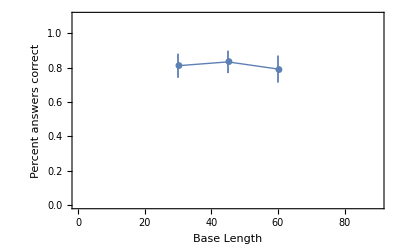

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,90},{0,1.1}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,1]],Mean@#[[;;,-1]]}&/@GatherBy[#,#[[{1}]]&]&/@DataClnGraded,{2,1,3}])
```

### Percent correct vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

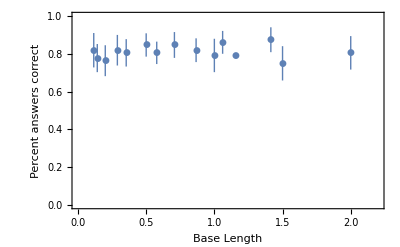

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0,1}},Frame-> {True,True,False,False},FrameLabel->{"Side Length","Percent answers correct"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@Transpose[Map[{(ToExpression@#[[1,2]])/Cos[ToExpression@#[[1,1]] Degree],Mean@#[[;;,-1]]}&,(GatherBy[#,#[[{1,2}]]&]&/@DataClnGraded),{2}],{2,1,3}])
```

### Response times vs. Base length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

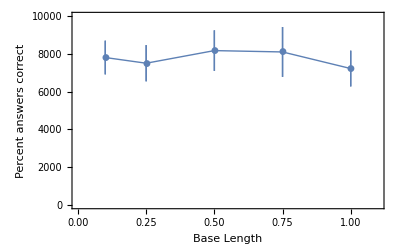

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,1.1},{0,1 10^4}},Frame-> {True,True,False,False},FrameLabel->{"Base Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,2]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{2}]]&]&/@DataClnGraded,{2,1,3}])
```

### Response Times vs. Angle Size

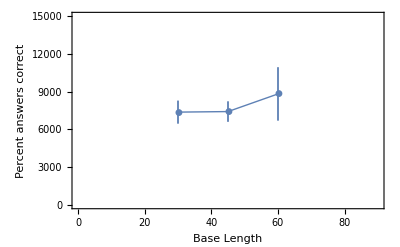

```mathematica
ErrorListPlot[#,Joined->True,PlotRange->{{0,90},{0,1.5 10^4}},Frame-> {True,True,False,False},FrameLabel->{"Angle Size [Deg]","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{ToExpression@#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]])]}&/@Transpose[{#[[1,1]],Median@ToExpression@#[[;;,7]]}&/@GatherBy[#,#[[{1}]]&]&/@DataClnGraded,{2,1,3}])
```

### Response Time vs. Side length

```mathematica
(*1=angle; 2=base factor; 3=Qtype; 4=Manipulation; 5=What's manipulated; 6=correct answer; 7=timing; 8=user answer; 9=correct/not*)
```

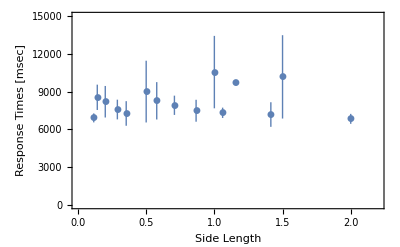

```mathematica
ErrorListPlot[#,(*Joined->True,*)PlotRange->{{0,2.2},{0,1.5 10^4}},Frame-> {True,True,False,False},FrameLabel->{"Side Length","Response Times [msec]"},PlotStyle->Thick,PlotMarkers->Automatic]&@({{#[[1,1]],Mean[#[[;;,2]]]},ErrorBar[N@(StandardDeviation[#[[;;,2]]]/(Sqrt@Length@#[[;;,2]]))]}&/@Transpose[Map[{(ToExpression@#[[1,2]])/Cos[ToExpression@#[[1,1]] Degree],Median@ToExpression@#[[;;,7]]}&,(GatherBy[#,#[[{1,2}]]&]&/@DataClnGraded),{2}],{2,1,3}])
```